```mathematica
alldata=Import[FileNameJoin[{NotebookDirectory[],"fixtures","output.csv"}]];
```

```mathematica
dataset=Import[FileNameJoin[{NotebookDirectory[],"fixtures","dataset.csv"}]];
```

```mathematica
holidays=DayRange[DateObject[{2014,1,1}],DateObject[{2015,12,31}],"Holiday",HolidayCalendar->{"UnitedStates", "Default"}];
```

```mathematica
extractDataByYear[l_List,y_Integer]:=Select[l,DateValue[First[#],"Year"]==DateValue[{y},"Year"]&]
```

```mathematica
extractDataByWeekday[l_List,w_Symbol]:=
Select[l,DayName[First[#]]==w&]
```

```mathematica
extractHourlyData[l_List]:=Map[Rest,l]
```

```mathematica
plotListWithModel[l_List,nlm_FittedModel]:=Show[Map[ListPlot,l],Plot[nlm[x],{x,0,24}],PlotRange->All,Ticks->{Range[24],Automatic}]
```

```mathematica
getSampleData[l_List,y_Integer,w_Symbol,n_Integer]:=extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,y],w]][[n]]
```

```mathematica
minMaxMeanPlot[l_List]:=Show[ListLinePlot[Map[Max,l],PlotStyle->Red],ListLinePlot[Map[Min,l],PlotStyle->Blue],ListLinePlot[Map[Mean,l],PlotStyle->Green],PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[getSampleData[dataset,2015,Monday,24],a+b x+c x^2+d x^3+e x^4,{a,b,c,d,e},x]
```

FittedModel[1110.41-1073.15 x+255.375 x^2-16.7501 x^3+0.329474 x^4]

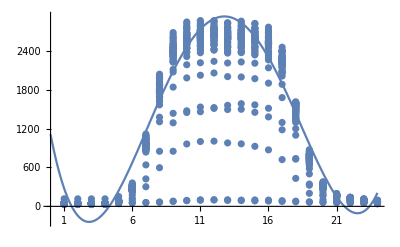

```mathematica
plotListWithModel[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2015],Monday]],nlm]
```

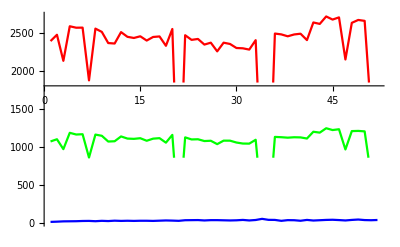

```mathematica
minMaxMeanPlot[extractHourlyData[extractDataByWeekday[extractDataByYear[dataset,2014],Monday]]]
```

```mathematica
(*Extract all data in mondays which max numbers of parking cars is greater than 2000*)
```

```mathematica
selectedMondays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[dataset,Monday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataBiased={DateValue[#1,"Hour"]}->#2&@@@Select[alldata,MemberQ[selectedMondays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pBiased=Predict[trainingdataBiased]
```

PredictorFunction[…]

```mathematica
(*Extract all data in mondays*)
trainingdataUnbiased={DateValue[#1,"Hour"],MemberQ[holidays,DateObject[DateList[#1][[1;;3]]]]}->#2&@@@Select[alldata,(DateValue[First[#],"Year"]==DateValue[{2014},"Year"]|| DateValue[First[#],"Year"]==DateValue[{2015},"Year"])&&DayName[First[#]]==Monday&]
```

{{0,False}→22,{1,False}→17,{2,False}→16,{4,False}→39,{5,False}→186,{6,False}→749,{3,False}→15,{7,False}→1529,{8,False}→2160,{9,False}→2316,{10,False}→2363,{11,False}→2394,{12,False}→2363,{13,False}→2359,2468,{10,False}→1001,{11,False}→1007,{12,False}→979,{13,False}→965,{14,False}→927,{15,False}→872,{16,False}→722,{17,False}→432,{18,False}→201,{19,False}→103,{20,False}→68,{21,False}→59,{22,False}→48,{23,False}→40}
 |  |  |  |

```mathematica
pUnbiased=Predict[trainingdataUnbiased,Method->"RandomForest"]
```

PredictorFunction[…]

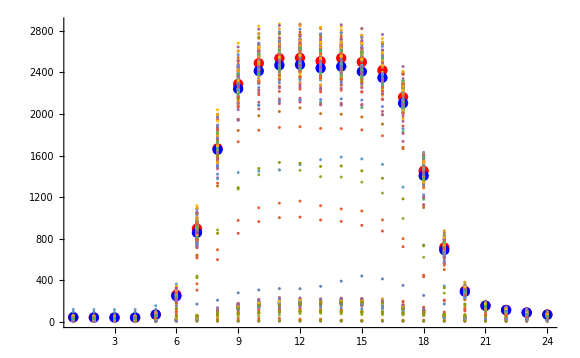

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[dataset,Monday]]],PlotRange->All]
```

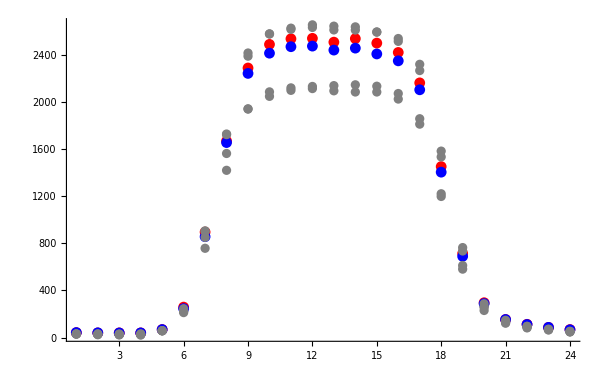

```mathematica
Show[ListPlot[Map[pBiased,Range[0,23]],PlotStyle->Red],ListPlot[Map[pUnbiased,{#,False}&/@Range[0,23]],PlotStyle->Blue],ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Monday]],PlotStyle->Gray],PlotRange->All]
```

```mathematica
data1415=Select[alldata,DateValue[First[#],"Year"]==DateValue[{2014},"Year"]||DateValue[First[#],"Year"]==DateValue[{2015},"Year"]&];
```

```mathematica
selectedTuesdays=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Tuesday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataTuesday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedTuesdays,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pTuesday=Predict[trainingdataTuesday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedWednesday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Wednesday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataWednesday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedWednesday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pWednesday=Predict[trainingdataWednesday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedThursday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Thursday],Max[Rest[#]]>2000&];
```

```mathematica
trainingdataThursday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedThursday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pThursday=Predict[trainingdataThursday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedFriday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Friday],Max[Rest[#]]>1600&];
```

```mathematica
trainingdataFriday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedFriday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pFriday=Predict[trainingdataFriday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedSaturday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Saturday],Max[Rest[#]]<145&];
```

```mathematica
trainingdataSaturday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedSaturday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pSaturday=Predict[trainingdataSaturday,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
selectedSunday=DateObject[DateList[First[#]][[1;;3]]]&/@Select[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Sunday],Max[Rest[#]]<155&];
```

```mathematica
trainingdataSunday={DateValue[#1,"Hour"]}->#2&@@@Select[data1415,MemberQ[selectedSunday,DateObject[DateList[First[#]][[1;;3]]]]&];
```

```mathematica
pSunday=Predict[trainingdataSunday,Method->"RandomForest"]
```

PredictorFunction[…]

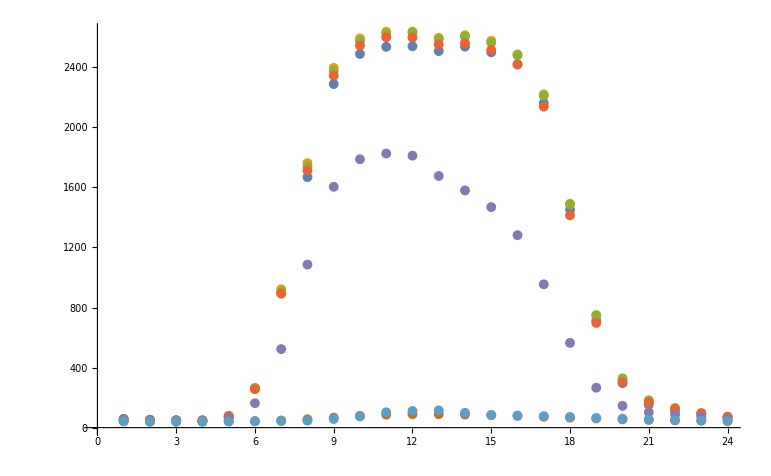

```mathematica
Show[ListPlot[{Map[pBiased,Range[0,23]],Map[pTuesday,Range[0,23]],Map[pWednesday,Range[0,23]],Map[pThursday,Range[0,23]],Map[pFriday,Range[0,23]],Map[pSaturday,Range[0,23]],Map[pSunday,Range[0,23]]}]]
```

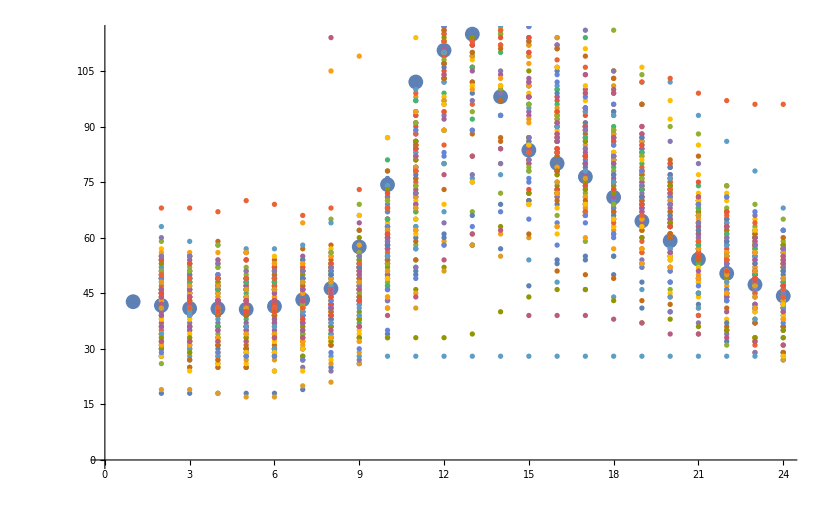

```mathematica
Show[ListPlot[Map[pSunday,Range[0,23]]],ListPlot[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Sunday]]]
```

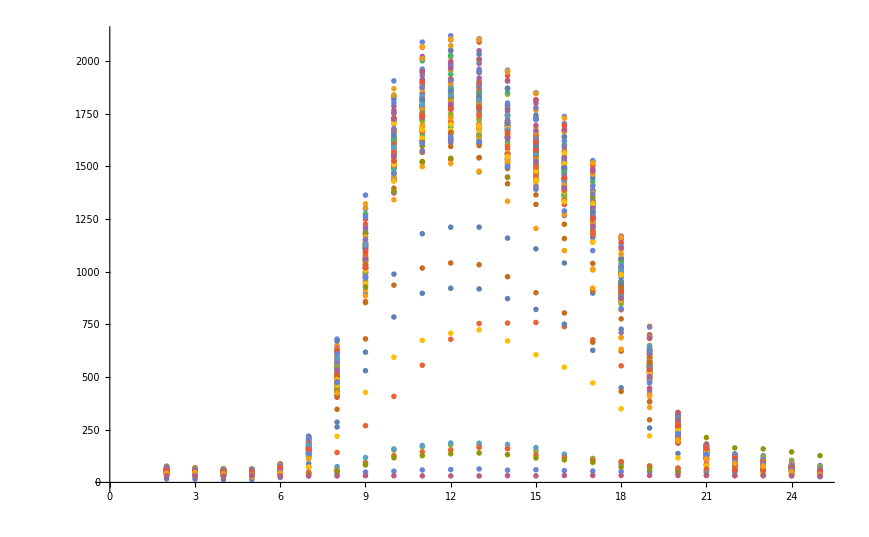

```mathematica
ListPlot[extractDataByWeekday[Join[extractDataByYear[dataset,2014],extractDataByYear[dataset,2015]],Friday]]
```

```mathematica
Map[pTuesday,Range[0,23]]
```

{52.9575,47.8472,45.1474,43.6435,75.3805,265.253,921.626,1762.22,2396.61,2592.25,2637.04,2637.17,2595.93,2613.34,2576.83,2485.75,2219.88,1491.4,744.384,318.049,170.009,122.289,94.2217,70.2105}

```mathematica
Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Tuesday]]
```

{{37,32,29,30,62,244,824,1607,2182,2375,2417,2426,2366,2359,2320,2236,1995,1328,607,234,125,91,70,56},{46,38,30,32,63,260,938,1840,2481,2678,2746,2761,2748,2770,2733,2639,2372,1666,877,405,270,210,186,167},{38,36,35,30,62,255,935,1746,2373,2601,2647,2676,2630,2651,2611,2541,2284,1597,833,323,175,121,84,64},{38,34,23,21,53,261,936,1792,2473,2674,2719,2692,2639,2651,2635,2570,2336,1605,809,303,140,94,69,47}}

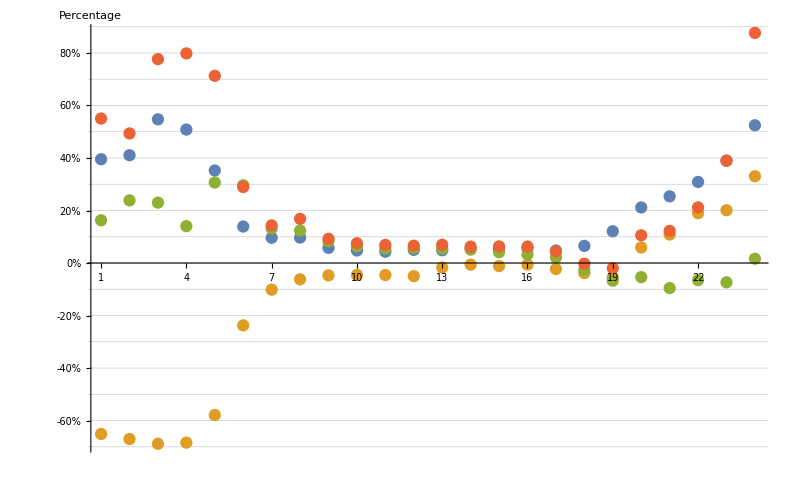

{{0,0%},{10,10%},{20,20%},{30,30%},{40,40%},{50,50%},{60,60%},{70,70%},{80,80%},{90,90%},{100,100%}}

```mathematica
ListPlot[100*(Subtract[Map[pWednesday,Range[0,23]],#]/#)&/@Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Wednesday]],AxesLabel->"Percentage",Ticks->{Range[1,24],{#,ToString[#]<>"%"}&/@Range[-100,100,10]},GridLines->{None,Range[-100,100,10]}, PlotRange->All]
```

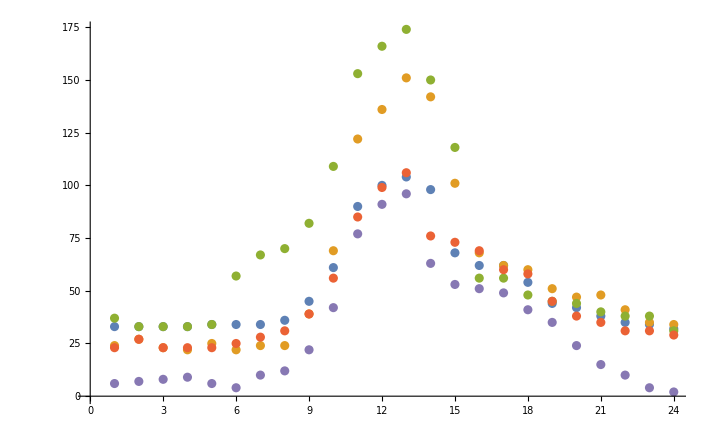

```mathematica
ListPlot[Map[Rest,extractDataByWeekday[extractDataByYear[dataset,2016],Sunday]]]
```